# Chapter 10

## 2D and 3D Graphics

## Visualizing Univariate Functions

## Using Free-Form Input

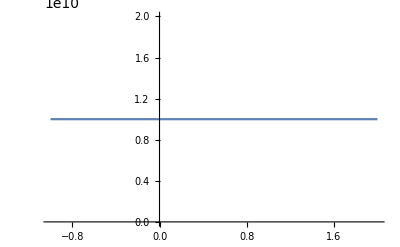

```mathematica
Plot[10^10, {x, -1, 2}]
```

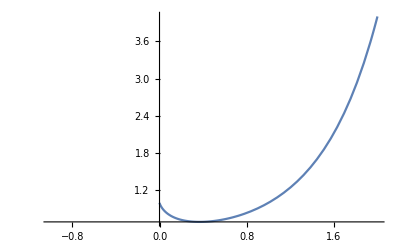

```mathematica
Plot[x^x, {x, -1,2}]
```

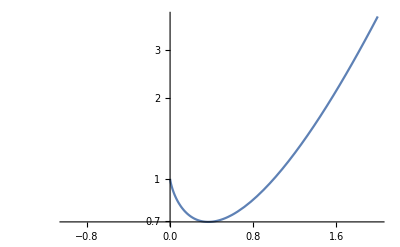

```mathematica
LogPlot[x^x, {x, -1, 2}]
```

WolframAlphaQueryParseResults

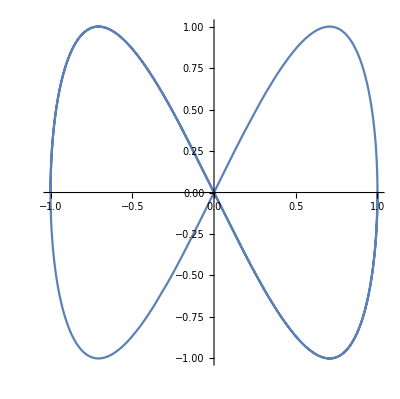

WolframAlphaQueryParseResults

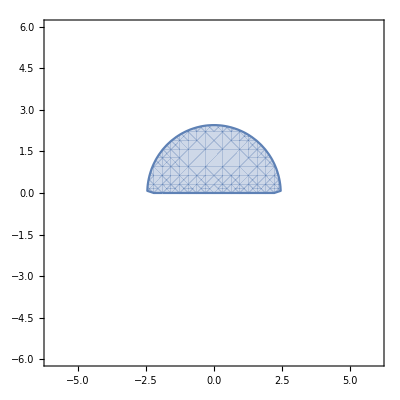

### Polar Plot

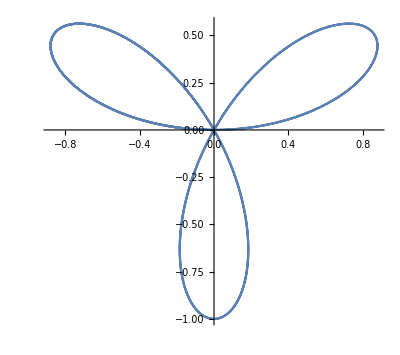

```mathematica
PolarPlot[Sin[3*t], {t, -1, 2*π}]
```

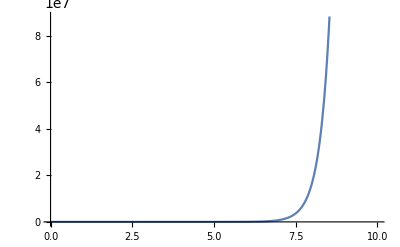

```mathematica
Plot[x^x,{x,0,10}]
```

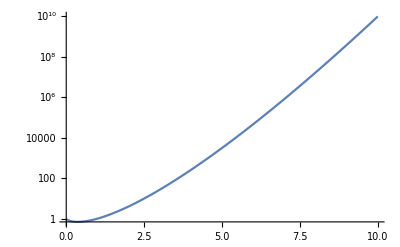

```mathematica
LogPlot[x^x,{x,0,10}]
```

## Plotting multiple functions together

WolframAlphaQueryParseResults

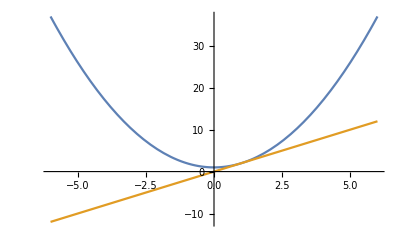

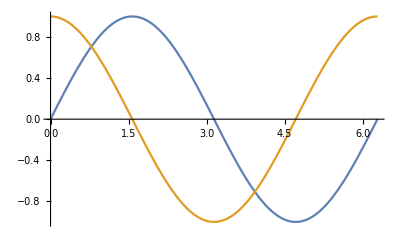

```mathematica
Plot[{Sin[x],Cos[x]},{x, 0,2π}]
```

## Plotting User-Defined Functions

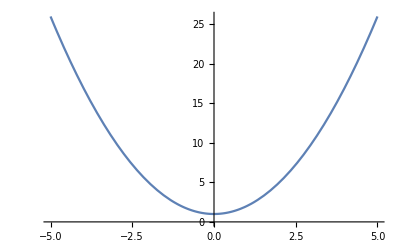

```mathematica
Plot[x^2+1,{x,-5,5}]
```

```mathematica
f[x_]:= x^2+1
```

```mathematica
Plot[f[x],{x,-5,5}]
```

-Graphics-

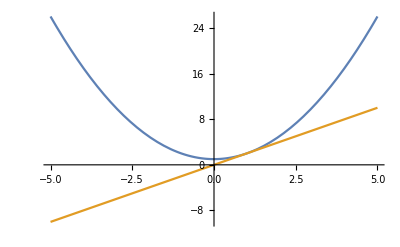

```mathematica
Plot[{f[x],f'[x]},{x,-5,5}]
```

```mathematica
h[x_]:= Piecewise[{{2x, x<0}, {x^2, 0 <= x <= 2}, {x, x>2}}]
```

```mathematica
h[x_]:=Piecewise[{{2 x,x<0},{x^2,0≤x≤2},{x,x>2}}]
```

SetDelayed::write: Tag Piecewise in (TagBox[GridBox[{{\"{\", GridBox[{{RowBox[{\"2\", \" \", \"x\"}], RowBox[{\"x\", \"<\", \"0\"}]},{SuperscriptBox[\"x\", \"2\"], RowBox[{\"0\", \"≤\", \"x\", \"≤\", \"2\"}]},{\"x\", RowBox[{\"x\", \">\", \"2\"}]},{\"0\", TagBox[\"True\",\"PiecewiseDefault\",AutoDelete->True]}
       },AllowedDimensions->{2, Automatic},Editable->True,GridBoxAlignment->{\"Columns\" -> {{Left}}, \"Rows\" -> {{Baseline}}},GridBoxItemSize->{\"Columns\" -> {{Automatic}}, \"Rows\" -> {{1.}}},GridBoxSpacings->{\"Columns\" -> {Offset[0.28], {Offset[0.84]}, Offset[0.28]}, \"Rows\" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}},Selectable->True]}
    },GridBoxAlignment->{\"Columns\" -> {{Left}}, \"Rows\" -> {{Baseline}}},GridBoxItemSize->{\"Columns\" -> {{Automatic}}, \"Rows\" -> {{1.}}},GridBoxSpacings->{\"Columns\" -> {Offset[0.28], {Offset[0.35]}, Offset[0.28]}, \"Rows\" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}}],\"Piecewise\",DeleteWithContents->True,Editable->False,SelectWithContents->True,Selectable->False,StripWrapperBoxes->True])[x_] is Protected.

$Failed

```mathematica
?*Form
```

```mathematica
FullForm[h[x]]
```

Piecewise[List[List[Times[2,x],Less[x,0]],List[Power[x,2],LessEqual[0,x,2]],List[x,Greater[x,2]]],0]

```mathematica
StandardForm[h[x]]
```

Piecewise[{{2 x, x<0}, {x^2, 0≤x≤2}, {x, x>2}, {0, True}}]

```mathematica
Plot[h[x]f,{x,-1,3}]
```

-Graphics-

```mathematica
h[x]
```

Piecewise[{{2 x, x<0}, {x^2, 0≤x≤2}, {x, x>2}, {0, True}}]

```mathematica
Clear[h]
```

```mathematica
h[x]
```

h[x]

```mathematica
h := Piecewise[{{2x, x<0}, {x^2, 0 <= x <= 2}, {x, x>2}}]
```

```mathematica
Plot[h[x],{x,-1,3}]
```

-Graphics-

```mathematica
h[-1]
```

(Piecewise[{{2 x, x<0}, {x^2, 0≤x≤2}, {x, x>2}, {0, True}}])[-1]

```mathematica
h[2]
```

(Piecewise[{{2 x, x<0}, {x^2, 0≤x≤2}, {x, x>2}, {0, True}}])[2]

```mathematica
Clear[h]
```

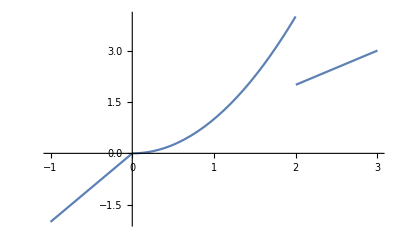

```mathematica
Plot[Piecewise[{{2x, x<0},{x^2, 0<= x<=2}, {x, x>2}}],
{x,-1,3}]
```



```mathematica
Plot[Sin[x], {x,0,2π}]
```

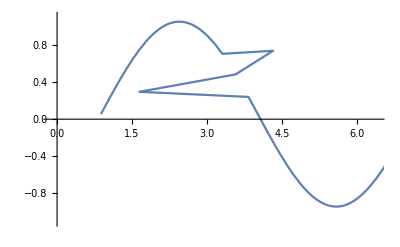

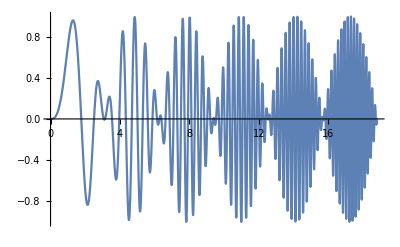

```mathematica
Plot[Sin[x]Sin[x^2], {x, 0, 6π}]
```

```mathematica
Plot3D[Sin[x y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{4+(3+Cos[v])Sin[u], 4+(3+Cos[v])Cos[u],
4+Sin[v]}, {u, 0,2π}, {v, 0,2π}]
```

```mathematica
Plot3D[Sin[x]Cos[y], {x,-3,3},{y,-3,3}, Mesh->All]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[x y], Cos[x y]},{x,-3,3},{y,-3,3}]
```

-Graphics3D-

## Other types of visualization

```mathematica
RevolutionPlot3D[Sin[t]Sin[t^2], {t, 0,π}]
```

-Graphics3D-

## Vector Plot

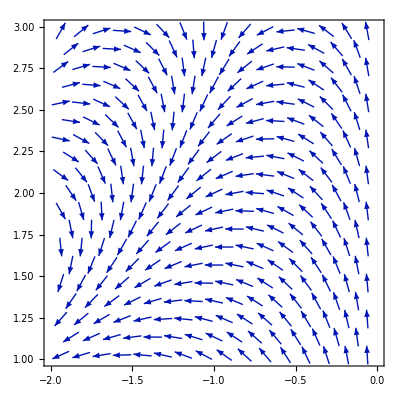

```mathematica
VectorPlot[{Sin[x y], Cos[x y]}, {x, -2, 0}, {y, 1,3}]
```

```mathematica
VectorPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

## Stream Plots

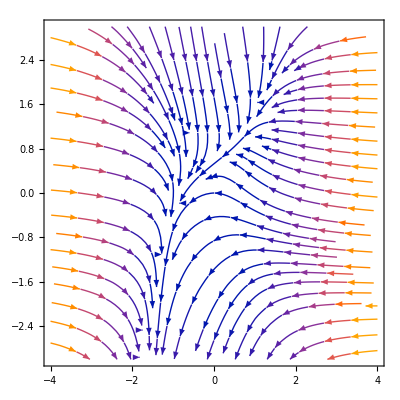

```mathematica
StreamPlot[{-1-x^3+y,x-y^2},
{x,-4,4},
{y,-3,3}]
```

```mathematica
Plot3D[{-1-x^3+y,x-y^2},
{x,-4,4},
{y,-3,3}]
```

-Graphics3D-

## Graphs

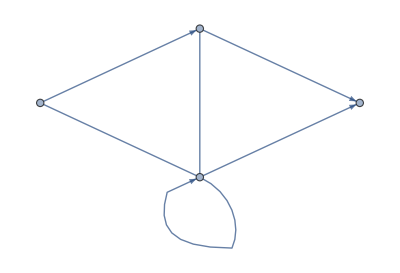

```mathematica
Graph[{1<->2,2<->3,3->1,2->4,1->4,2->2}]
```

```mathematica
a = 1.111111111111111111
```

1.11111111111111111

```mathematica
Do[2a-1,{55}]
```

```mathematica
a
```

1.11111111111111111

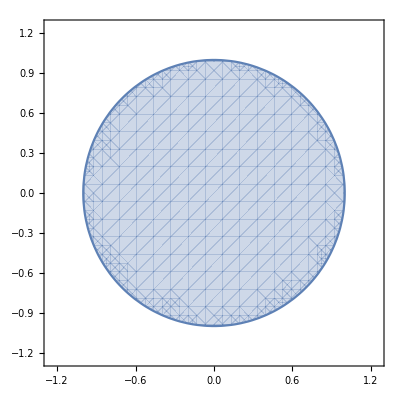

```mathematica
RegionPlot[x^2+y^2<= 1, {x, -1.25,1.25},{y,-1.25,1.25},Axes->True]
```

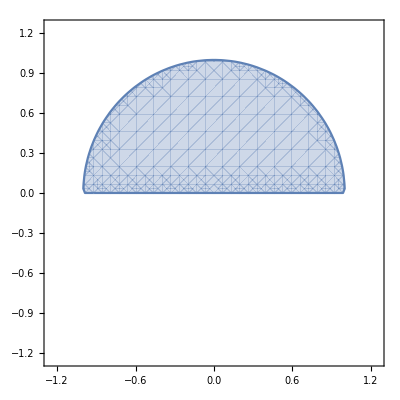

```mathematica
RegionPlot[x^2+y^2<= 1 && y >= 0, {x,-1.25,1.25},{y,-1.25,1.25},Axes -> True]
```

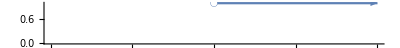

```mathematica
NumberLinePlot[x>1,{x,0,2}]
```

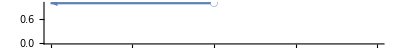

```mathematica
NumberLinePlot[x<1,{x,0,2}]
```

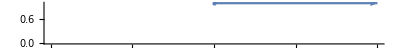

```mathematica
NumberLinePlot[x>=5, {x,0,10}]
```

```mathematica
NumberLinePlot[Interval[{5,Infinity}]]
```

-Graphics-

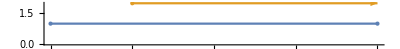

```mathematica
NumberLinePlot[{Interval[{1,5}],Interval[{2,∞}]}]
```

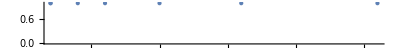

```mathematica
NumberLinePlot[Fibonacci[Range[7]]]
```

```mathematica
Manipulate[NumberLinePlot[Fibonacci[Range[x]]],{x,1,60}]
```

```mathematica
Manipulate[RegionPlot[x^2+y^3<n, {x,-2,2},{y,-2,2}],
{n,-1,1}]
```

```mathematica
Clear[f,h]
```

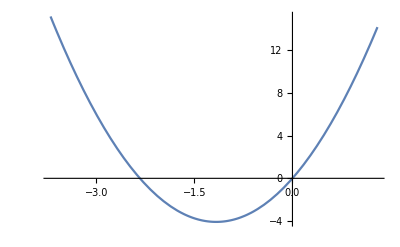

```mathematica
Plot[3*x^2 + 7*x , {x, -3.7, 1.3}]
```

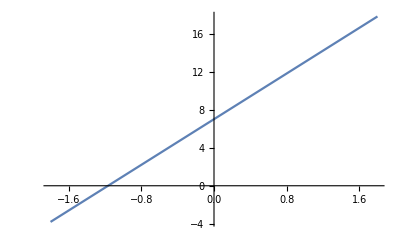

```mathematica
Plot[Evaluate[D[3*x^2 + 7*x - 9, x]], {x, -1.8, 1.8}]
```

```mathematica
Show[Show[%28,AxesStyle->Gray],AxesStyle->Gray]
```

-Graphics-

WolframAlphaQueryParseResults

-Graphics3D-

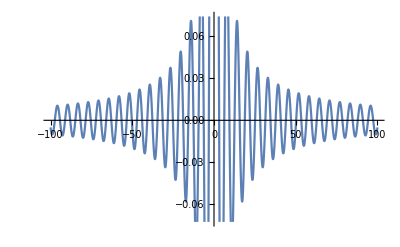

```mathematica
Plot[Sin[x]/x,{x,-100,100}]
```

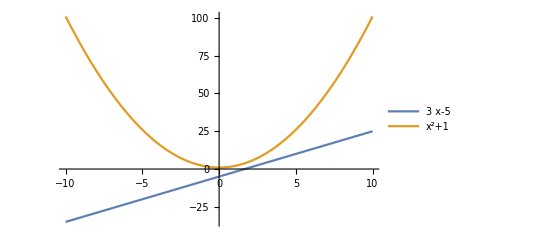

```mathematica
Plot[{3x-5,x^2+1},{x,-10,10},PlotLegends->"Expressions"]
```

```mathematica
f[x_]:= 3x-5
```

```mathematica
h[x_]:= x^2+1
```

```mathematica
Plot[{f[x],h[x]},{x,-10,10}, PlotLegends->{f[x],h[x]}]
```

-Graphics-

```mathematica
Plot3D[Sin[x]Cos[x]Sin[y],{x,-π,π}, {y,-π,π}]
```

-Graphics3D-

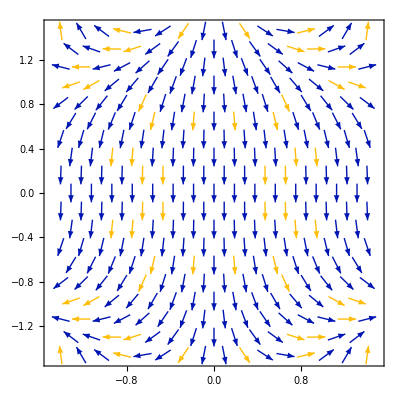

```mathematica
VectorPlot[{3Sin[x y^2],-3Cos[x y^2]}, {x,-1.5,1.5},{y,-1.5,1.5}]
```

```mathematica
N[3Sin[1 1]]
```

2.52441

```mathematica
Graph[{1->2,1->3,1->4,2->3,2->5,3->1,3->3,3->5,4->1,4->5, 5->5}]
```

-Graphics-

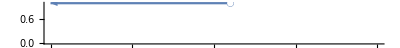

```mathematica
NumberLinePlot[x<1/2,{x,-5,5}]
```

```mathematica
Manipulate[NumberLinePlot[x<=number,{x,-5,5}],{number, 0, 5}]
```